```mathematica
Advanced Plotting in Mathematica
```

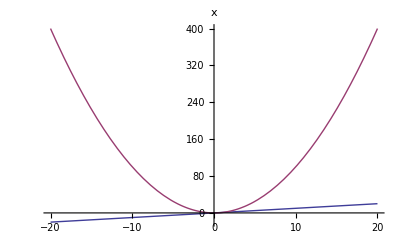

```mathematica
Plot[{x,x^2,X^3},{x,-20,20},{PlotLabel->Style[x,Blue],PlotLabel->Style[x^2,Red,20]}]
```

```mathematica
Table[Plot[Evaluate[f[x]],{x,-5,5},PlotLabel->f[x]],{f,{Sin,Cos,Csc,Sec,Tan,Cot}}]
```

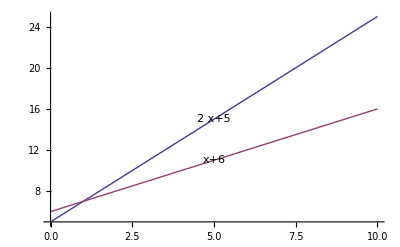

```mathematica
fns[x_]:={5+2 x,6+x};
len:=Length[fns[x]];

Plot[Evaluate[fns[x]],{x,0,10},Epilog->Table[Inset[Framed[DisplayForm[fns[x][[i]]],RoundingRadius->5],{5,fns[5][[i]]},Background->White],{i,len}]]
```

```mathematica
DynamicModule[{pos=Table[{1,fns[1][[i]]},{i,len}]},LocatorPane[Dynamic[pos],Plot[Evaluate[fns[x]],{x,0,10}],Appearance->Table[Framed[Text@TraditionalForm[fns[x][[i]]],RoundingRadius->5,Background->White],{i,len}]]]
```

## Labeling curves in plots

There are times when you want to label curves in plots and would like an easy way to do it. The function defined here allow you to do that. It takes the option CurveLabel where the labels can be given as text or {text, position} where position is given as a fraction of the distance across the plot. The default puts the label in the center of the plot.

### The function

```mathematica
LabelPlot[func_List,{var_,varmin_,varmax_},opts___?OptionQ]:= Module[{crvlbl,pltopts,funclis,txt,tt,aa,f},
crvlbl = CurveLabel/.{opts}/.CurveLabel -> None;
pltopts = Select[{opts},#[[1]]=!=CurveLabel&];
funclis = Table[f[i][tt_]=If[Head[func[[i]]]===Symbol&&func[[i]]=!=var,func[[i]][tt],func[[i]]/.var->tt],{i,Length[func]}];
txt = Table[If[Head[crvlbl[[i]]] ===List, Text[StyleForm[ToString[crvlbl[[i,1]]],Background -> GrayLevel[.95],FontSize -> 10],{aa[i]=crvlbl[[i,2]] (varmax-varmin),f[i][aa[i]]},{0,-1}],Text[StyleForm[ToString[crvlbl[[i]]],Background -> GrayLevel[.95],FontSize -> 10],{aa[i]= (varmax-varmin)/2,f[i][aa[i]]},{0,-1}]],{i,Length[crvlbl]}];
Plot[Evaluate[Table[f[i][rr],{i,Length[func]}]],{rr,varmin,varmax},Epilog -> txt,Evaluate[pltopts]]
];
LabelPlot[func_,{var_,varmin_,varmax_},opts___?OptionQ]:= Module[{crvlbl,pltopts,f1,txt,tt,aa},
crvlbl = CurveLabel/.{opts}/.CurveLabel -> None;
pltopts = Select[{opts},#[[1]]=!=CurveLabel&];
f1[tt_]=If[Head[func]===Symbol&&func=!=var,func[tt],func/.var->tt];
txt = If[Head[crvlbl] ===List, Text[StyleForm[ToString[crvlbl[[1]]],Background -> GrayLevel[.95],FontSize -> 10],{aa=crvlbl[[2]] (varmax-varmin),f1[aa]},{0,-1}],Text[StyleForm[ToString[crvlbl],Background -> GrayLevel[.95],FontSize -> 10],{aa= (varmax-varmin)/2,f1[aa]},{0,-1}]];
Plot[f1[tt],{tt,varmin,varmax},Epilog -> txt,Evaluate[pltopts]]
]
```

### Some examples

A single curve.

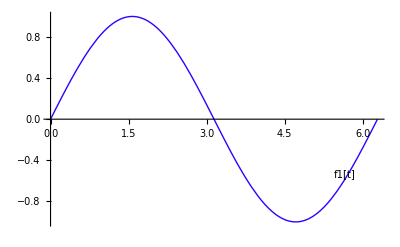

```mathematica
LabelPlot[Sin[x],{x,0,2 π},PlotStyle-> Hue[.7],CurveLabel -> {f1[t],.9}]
```

### More than one curve

As programmed here you must have the same number of curve labels as you do curves.

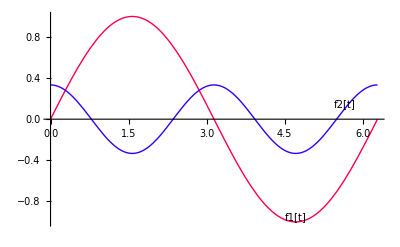

```mathematica
myplt3 = LabelPlot[{Sin[x],Cos[2 x]/3},{x,0,2 π},PlotStyle->{Hue[.95], Hue[.7]},CurveLabel ->{ {f1[t],3/4},{f2[t],.9}},PlotRange -> {{0, 2 π},{-1,1}}]
```

### Making changes and limitations

You can easily change the way the text appears by finding the four occurrences of StyleForm and making the appropriate changes in each. Because the labels are executed using Epilog this will not work using Show. You will only get the labels from the first plot in the Show argument.